```mathematica
η=1*10^-2;
dt=0.1;
T=295;
dx=16.0*10^-7/32
v=dx^3;
kb=1.3806*10^-16;
R=(6.6365*10^-8);
```

5.×10^-8

```mathematica
χ=(kb T)/(6 π η R)
```

3.25574×10^-6

```mathematica
((2 χ)/dx^2)^-1
```

3.83937×10^-10

```mathematica
χ*1.01
```

7.92403×10^-6

```mathematica
((1.6*10^-19)^2)/((8*10^-7)^2)
```

4.×10^-26

```mathematica
1/(8*10^-7)
```

```mathematica
dx=(25*10^-7)/64;
F=1;
V=(25*10^-7)^3;
U=142076186.21676001;

araw=Solve[F==6 π η a U (1.0+1.7601 ((4/3 π a^3)/V)^(1/3)),a][[1,1,2]];
araw/dx
```

0.91851

```mathematica
χ=(kb T)/(6 π η R)
```

6.51148×10^-6

```mathematica
Solve[6 π η Rt == 6 π η Rw + 6 π η Rd,Rd]
```

{{Rd→Rt-Rw}}

```mathematica
Clear[srf]
eps =1*10^-16; σ=5*10^-8;q=4.8*10^-10;
srf[r_]=4 eps ((6 (σ/2)^6)/r^7-(12 (σ/2)^12)/r^13);
cf[r_]=-q^2/r^2;
```

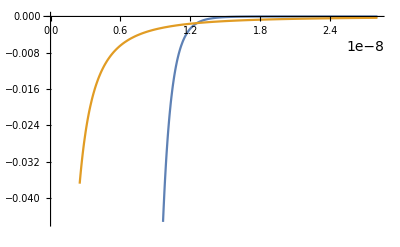

```mathematica
Plot[{srf[r],cf[r]},{r,0.1(σ/2),1.122(σ/2)},AxesOrigin->{0,0}]
```

```mathematica
dd=5.0*10^-8;
srf[dd]
cf[dd]/q
```

7.26563×10^-10

-192000.

```mathematica
DX=1*10^-4;
DY=DX;
DZ=DX;
dx=DX/4;
dy=DY/4;
dz=DZ/4;
litre=10^6;
TV=DX*DY*DZ;
molarity=0.01;

NN=(TV/litre)*6.02*10^23*molarity
```

6020.

```mathematica
NN/TV
```

6.02×10^15

```mathematica
currentDensity=111.6
eField=1 10^12;
2*currentDensity/eField
```

111.6

1.116×10^-10

```mathematica
kb T
```

4.07277×10^-14

```mathematica
0.001*6.02*10^23
```

6.02×10^20